```mathematica
AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];
```

```mathematica
AWD=DeleteCases[DeleteCases[AllWidthData,AllWidthData[[1]]],{}];
```

```mathematica
db=0.2;bins=Table[x,{x,0,3,db}];
```

```mathematica
ic=1;
WDtest=Select[AWD,(#1[[3]]==ic)&];
```

```mathematica
nw=Length[WDtest]
```

80

```mathematica
Warray=Table[WDtest[[i,7]],{i,1,nw}];
```

```mathematica
meanw=Mean[Warray]
```

0.00228744

```mathematica
wc1=BinCounts[Warray/meanw,{bins}]
```

{21,14,6,9,3,6,3,1,1,2,1,1,1,1,2}

```mathematica
wcnorm=Table[{bins[[i]],wc1[[i]]/nw/db},{i,1,Length[bins]-1}]
```

{{0.,1.3125},{0.2,0.875},{0.4,0.375},{0.6,0.5625},{0.8,0.1875},{1.,0.375},{1.2,0.1875},{1.4,0.0625},{1.6,0.0625},{1.8,0.125},{2.,0.0625},{2.2,0.0625},{2.4,0.0625},{2.6,0.0625},{2.8,0.125}}

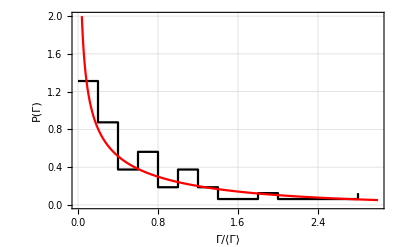

```mathematica
pporterthomas=Show[ListPlot[wcnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[Exp[-x/2]/(√(2π x)),{x,0,3},PlotStyle->Red,PlotRange->{0,2}],PlotRange->{0,2},Frame->True,GridLines->Automatic,FrameLabel->{"Γ/⟨Γ⟩","P(Γ)"},LabelStyle->Large]
```

```mathematica
c1=Table[{Log[WDtest[[ires,6]]],Warray[[ires]]/meanw},{ires,1,Length[WDtest]}]
```

{{7.69644,0.150771},{7.2203,0.476378},{5.09547,4.9434},{8.68896,0.184828},{7.43603,0.705029},{6.88026,1.34726},{6.59967,1.80888},{10.1194,0.0563961},{7.7463,0.65132},{9.93639,0.075945},{10.8437,0.0324849},{6.14951,3.62748},{7.35756,1.15221},{6.36021,3.25388},{7.21664,1.41309},{8.08212,0.597211},{7.97474,0.676414},{8.69758,0.336607},{11.6748,0.0177839},{9.0405,0.249951},{9.29753,0.199702},{6.30994,4.12886},{12.7737,0.00647175},{8.98866,0.293538},{9.93591,0.116991},{7.53658,1.29021},{11.2081,0.032587},{9.56015,0.174318}}

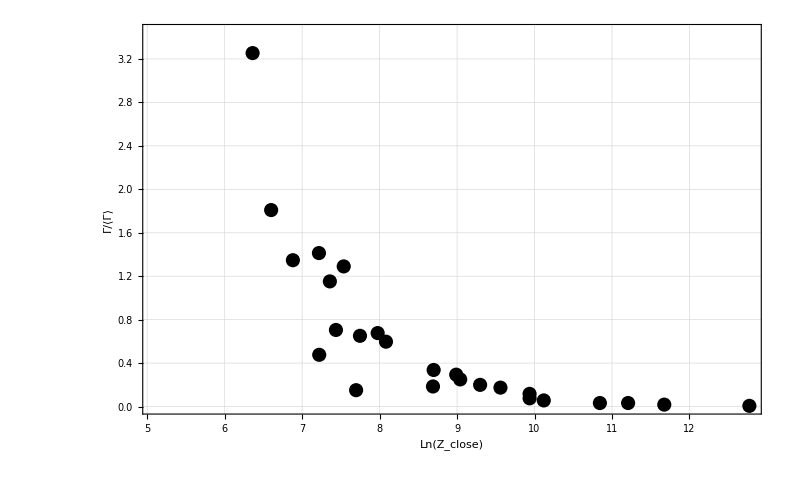

```mathematica
pc1=ListPlot[c1,Frame->True,LabelStyle->Large,FrameLabel->{"Ln(Z_close)","Γ/⟨Γ⟩"},PlotStyle->Black,GridLines->Automatic]
```